# Fitting the copula

## Introduction

Idea: Fit copula according to copula dependence measures, such as Spearman’s rho (rank correlation), Kendalls’ tau and quantile dependence, see e.g. Oh and Patton (2013) (screenshot below). This method is called “method of moments” in the literature. See also McNeil et al. (2005), Section 5.5. Note also the empirical DF variant, which ensures that the data lie strictly in the interior of the unit cube (page 232 of McNeil et al, 2005). See also Nelsen (2006). See Fermanian et al. (2004) for convergence of the sample measures to their population counterparts. 

Possibly use the following dependence measures for calibration: rank correlation, 0.05, 0.1, 0.9, 0.95 quantile dependence (this is what Oh and Patton (2013) use). 

-Graphics-

## Basic functions

```mathematica
Clear["Global`*"]
```

```mathematica
Clear[α,β,μ,δ,μ1,μ2,δ1,δ2]
```

Density function

```mathematica
q[x_]:=√(1+x^2);
g[x_,α_,β_,μ_,δ_]:=(α Exp[δ √(α^2-β^2)-β μ] BesselK[1,δ α q[(x-μ)/δ]] Exp[β x])/(π q[(x-μ)/δ]);
```

Moment-generating function

```mathematica
M[u_,α_,β_,μ_,δ_]:=Exp[δ (√(α^2-β^2)-√(α^2-(β+u)^2))+μ u]
```

Standardize NIG PDF’s by setting location and scale

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

The NIG is implemented in Mathematica as a Generalised Hyperbolic distribution

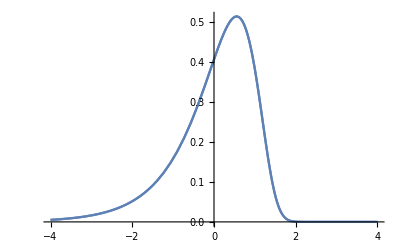
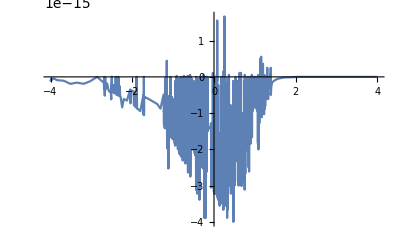

```mathematica
{Plot[{g[x,α,β,μs[α,β],δs[α,β]],PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]}/.{α->10, β->-9}, {x,-4,4},PlotRange->All],
Plot[{g[x,α,β,μs[α,β],δs[α,β]]-PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]}/.{α->10, β->-9}, {x,-4,4},PlotRange->All]
}
```

NIG factor copula
-Graphics-

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_,α_,β_]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Joint distribution function (factor model)
-Graphics-

```mathematica
F2NIG[x_,y_,α_,β_,μ1_,μ2_,δ_,δ1_,δ2_]:=
NIntegrate[FNIG[x-z,α,β,μ1,δ1] FNIG[y-z,α,β,μ2,δ2] fNIG[z,α,β,0,δ], {z,-∞, ∞}]
```

```mathematica
{Timing[FNIG[0.5,5,0.1,0,0.5]], Timing[NIGCDF[0.5, 5, 0.1]]}
```

(0.024197 | 0.942472
0.008394 | 0.694353)

```mathematica
{Timing[fNIG[0.5,5,0.1,0,0.5]], Timing[NIGPDF[0.5, 5, 0.1]]}
```

(0.00095 | 0.307374
0.000414 | 0.353738)

```mathematica
{Timing[InvFNIG[0.9, 5, 0.1,0,0.5]], Timing[NIGInv[0.9, 5, 0.1]]}
```

(0.015436 | 0.394356
0.016024 | 1.27435)

```mathematica
Timing[F2NIG[0.5,0.1,5,0,0,0,1,0.5,0.5]]
```

{5.52639,0.547637}

## Copula dependence measures

NIG factor copula
-Graphics-

```mathematica
CNIG[u_,v_,α_,β_,δ_]:=F2NIG[NIGInv[u,α,β],NIGInv[v,α,β],α,β,μs[α,β],μs[α,β],δ,δs[α,β]-δ,δs[α,β]-δ]
```

```mathematica
Timing[CNIG[0.5,0.1,5,0,1]]
```

{4.03301,0.0638757}

```mathematica
Timing[CNIG[0.5, 0.1, 5,4,1]]
```

{18.5246,0.0985602}

### Spearman’s Rho -Graphics-

Multiple uses of NIntegrate are extremely inefficient, in addition CNIG is slow, therefore the function below is not  an option.

```mathematica
Rho[α_,β_,δ_]:=
12 NIntegrate[CNIG[u,v,α,β,δ], {u,0,1}, {v,0,1}]-3
```

This one is numerically highly unstable

```mathematica
Rho[α_,β_,δ_]:=Module[{},
12 NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μs[α,β],δs[α,β]-δ] FNIG[NIGInv[v,α,β]-z,α,β,μs[α,β],δs[α,β]-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞}, {u,0,1}, {v,0,1}]-3
]
```

This one is also slow and numerically unstable

```mathematica
Rho[α_,β_,δ_]:=Module[{μ1,δ1},
μ1=μs[α,β];
δ1=δs[α,β];
12NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0,0.5}, {v,0,0.5},PrecisionGoal->2] \
+ NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0.5,1.}, {v,0,0.5},PrecisionGoal->2] \
+  NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0,0.5}, {v,0.5,1.},PrecisionGoal->2] \
  + NIntegrate[FNIG[NIGInv[u,α,β]-z,α,β,μ1,δ1-δ] FNIG[NIGInv[v,α,β]-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ], {z,-∞, ∞},{u,0.5,1.}, {v,0.5,1.},PrecisionGoal->2]-3
]
```

```mathematica
(*Timing[Rho[5,1,4]]*)
```

First, re-write Spearman’s rho in terms of the distribution functions avoiding calls to inverse CDF. 
Second, use interpolation to speed up CDF calculations

-Graphics-

This implements the first step

```mathematica
Rho[α_,β_,δ_]:=Module[{μ1,δ1},
μ1=μs[α,β];
δ1=δs[α,β];
12 NIntegrate[FNIG[x-z,α,β,μ1,δ1-δ] FNIG[y-z,α,β,μ1,δ1-δ] fNIG[z,α,β,0,δ]NIGPDF[x,α,β] NIGPDF[y,α,β], {z,-∞, ∞},{x,-∞, ∞},{y,-∞, ∞},PrecisionGoal->2]-3
]
```

```mathematica
Clear[α,β,δ]
α=5;
β=α-1;
sol=NSolve[δ/δs[α,β]==0.2,δ];
δ=δ/.sol[[1]];
```

```mathematica
(*Timing[Rho[α,β,δ]]*)
```

Now for the interpolation

```mathematica
Clear[FNIGi]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
Fi=FNIGi[5,4,μs[5,4], δs[5,4]]
```

InterpolatingFunction[…]

```mathematica
{Timing[FNIG[0.9, 5,4,μs[5,4],δs[5,4]]], Timing[NIGCDF[0.9, 5,4]], Timing[Fi[0.9]]}
```

(0.024471 | 0.842564
0.022698 | 0.842564
0.00001 | 0.842567)

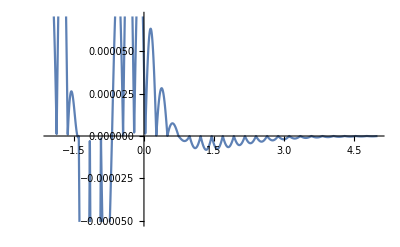
{38.066,-Graphics-}

```mathematica
Timing[Plot[{FNIG[x,5,4,μs[5,4],δs[5,4]]-Fi[x]}, {x,-2,5}]]
```

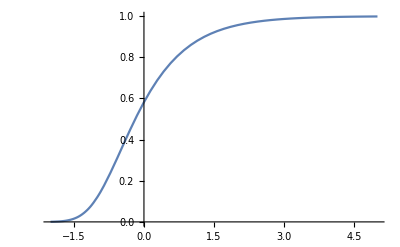
{0.019039,-Graphics-}

```mathematica
Timing[Plot[Fi[x], {x,-2,5}]]
```

```mathematica
Clear[α,β,δ]
α=5;
β=α-1;
sol=NSolve[δ/δs[α,β]==0.2,δ];
δ=δ/.sol⟦1⟧;
```

```mathematica
Clear[Rho]
```

```mathematica
Rho[α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{μ1,δ1,Fi},
μ1=μs[α,β];
δ1=δs[α,β];
Fi=FNIGi[α,β,μ1,δ1-δ];
12 NIntegrate[Fi[x-z] Fi[y-z] fNIG[z,α,β,0,δ]NIGPDF[x,α,β] NIGPDF[y,α,β], {z,-∞, ∞},{x,-∞, ∞},{y,-∞, ∞},PrecisionGoal->2]-3
]
```

```mathematica
Timing[Rho[α,β,δ]]
```

{1.31941,0.18105}

### Quantile dependence

Speed up copula function by reducing precision

```mathematica
Clear[F2NIG2, QD, CNIG2]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ]:=
Module[{F1,a,b},
F1=FNIGi[α,β,μ1,δ1];
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
{Timing[F2NIG[0,0,5,0,0,0,1,1,1]], Timing[F2NIG2[0,0,5,0,0,1,1]]}
```

(2.36939 | 0.333333
1.16867 | 0.333327)

```mathematica
Clear[F1]
F1=FNIGi[5,1,0,1];
```

```mathematica
{Timing[F2NIG[0,0,5,1,0,0,1,1,1]], Timing[F2NIG2[0,0,5,1,0,1,1,F1]]}
```

(2.80728 | 0.13066
0.207267 | 0.13066)

```mathematica
{Timing[F2NIG[0,0,5,1,0,0,1,1,1]], Timing[F2NIG2[0,0,5,1,0,1,1]]}
```

(2.79486 | 0.13066
1.31133 | 0.13066)

```mathematica
Timing[F2NIG2[0,0.5,5,1,0,1,1]]
```

{1.51599,0.213968}

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
{Timing[CNIG[0.5,0.2,5,1,1]], Timing[CNIG2[0.5, 0.2, 5,1,1]]}
```

(4.28821 | 0.123443
1.23383 | 0.123445)

```mathematica
Timing[F1=FNIGi[5,1,μs[5,1],δs[5,1]-1];]
```

{0.782073,Null}

```mathematica
{Timing[CNIG2[0.5,0.2,5,1,1]], Timing[CNIG2[0.5, 0.2, 5,1,1,F1]]}
```

(1.22767 | 0.123445
0.430044 | 0.123445)

```mathematica
Timing[Table[CNIG2[0.5,k, 5,1,1,F1], {k,{0.1, 0.2}}]]
```

{0.884279,{0.0645138,0.123445}}

```mathematica
Timing[{CNIG2[0.5,0.1, 5,1,1],CNIG2[0.5,0.2, 5,1,1]}]
```

{2.46668,{0.0645138,0.123445}}

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ]/q,(1-2q+ CNIG2[q,q,α,β,δ])/(1-q)]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

```mathematica
Timing[QD[0.1, 5,2,1]]
```

{1.23271,0.194345}

```mathematica
Clear[F1]
F1=FNIGi[5,2,μs[5,2],δs[5,2]-1];
```

```mathematica
Timing[QD[0.1, 5,2,1,F1]]
```

{0.282832,0.194345}

```mathematica
Timing[QD[0.9, 5,2,1]]
Timing[QD[0.9,5,2,1,F1]]
```

{1.20572,0.209888}

{0.266457,0.209888}

```mathematica
Timing[Table[QD[q,5,0,1], {q,{0.05,0.1, 0.9, 0.95}}]]
Timing[F1=FNIGi[5,0,μs[5,0], δs[5,0]-1];Table[QD[q,5,0,1,F1], {q,{0.05,0.1, 0.9, 0.95}}]]
```

{3.84124,{0.108669,0.174513,0.174466,0.108663}}

{1.57443,{0.108669,0.174513,0.174466,0.108663}}

```mathematica
Timing[Table[QD[q,5,4,1], {q,{0.05,0.1, 0.9, 0.95}}]]
Timing[F1=FNIGi[5,4,μs[5,4], δs[5,4]-1];Table[QD[q,5,4,1,F1], {q,{0.05,0.1, 0.9, 0.95}}]]
```

{6.72757,{0.710377,0.755312,0.831138,0.815893}}

{2.44878,{0.710377,0.755312,0.831138,0.815893}}

## Empirical measures

```mathematica
α=5; 
β=3;
δ=1;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
SeedRandom[123456];
n=50000;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
{Mean[X1],Mean[X2]}
{Variance[X1], Variance[X2]}
```

{0.00473222,0.00114526}

{1.00042,1.00099}

Correlation

```mathematica
N[{δ/δs[α,β],Correlation[X1,X2]}]
```

{0.390625,0.391036}

Rank correlation

```mathematica
N[{(6 ArcSin[δ/(2 δs[α,β])])/π,(6 ArcSin[1/2 Correlation[X1,X2]])/π,Rho[α,β,δ],SpearmanRho[X1,X2]}]
```

{0.375433,0.375833,0.373419,0.373606}

Quantile  dependence

Empirical DF (values lie strictly in [0,1])

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
s=Sort[X1];
```

```mathematica
q1=Sort[X1]⟦Round[0.95 Length[X1]]⟧;
q2=Sort[X2]⟦Round[0.95 Length[X2]]⟧;
sel=Select[{X1,X2}ᵀ, #1[[1]]<q1 && #1[[2]]<q2&];
```

```mathematica
Length[sel]/(0.95Length[X1])
```

0.959095

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sell},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
{QDemp[0.05,X1,X2],QD[0.05, α, β,δ]}
```

{0.1724,0.17475}

```mathematica
{QDemp[0.95,X1,X2], QD[0.95, α,β,δ]}
```

{0.2236,0.223989}

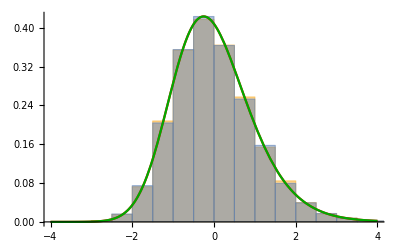

```mathematica
Show[
Histogram[{X1,X2}, Automatic, "PDF"],
Plot[{fNIG[x,α,β, μs[α,β], δs[α,β]],NIGPDF[x,α,β]}, {x,-4,4},PlotStyle->{Red,Darker[Green]}]
]
```

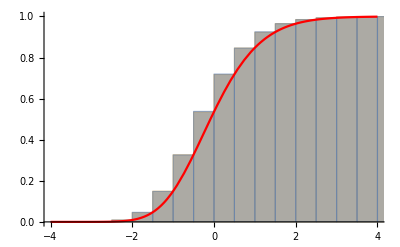

```mathematica
Fi=FNIGi[α,β,μs[α,β], δs[α,β]];
Show[
Histogram[{X1,X2}, Automatic, "CDF"],
Plot[Fi[x],  {x,-4,4},PlotStyle->Red]
]
```

```mathematica
Fi=FNIGi[α,β,μs[α,β], δs[α,β]]
u1=Table[Fi[X1[[k]]], {k,1,Length[X1]}];
```

InterpolatingFunction[…]

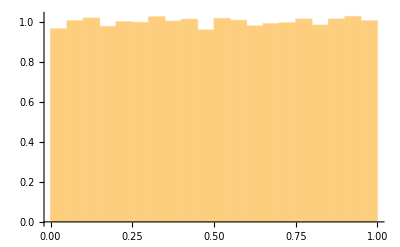

```mathematica
Histogram[u1, Automatic, "PDF"]
```

This is extremely slow (see small number of simulations):

```mathematica
U=RandomVariate[UniformDistribution[],1000];
Timing[N1=N[NIGInv[U,α,β]];]
```

{7.39779,Null}

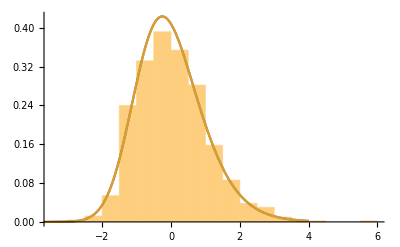

```mathematica
Show[
Histogram[N1, Automatic, "PDF"],
Plot[{fNIG[x, α, β, μs[α,β], δs[α,β]],NIGPDF[x,α,β]}, {x,-4,4}]
]
```

```mathematica
{F2NIG2[1,1,α,β,μs[α,β],δ,δs[α,β]-δ],N[1/Length[X1] Length[Select[Transpose[{X1,X2}],#1⟦1⟧<1&&#1⟦2⟧<1&]]]}
```

{0.748324,0.74626}

## Fit simulated data

```mathematica
{Length[X1], Length[X2]}
```

{50000,50000}

```mathematica
x1=X1;
x2=X2;
```

```mathematica
rs=SpearmanRho[x1,x2]
```

0.373606

```mathematica
Table[QDemp[q,x1, x2], {q, {0.05, 0.1, 0.9, 0.95}}]
```

{0.1724,0.2508,0.2948,0.2236}

```mathematica
{α,β,μ,δ}
```

{5,3,0,1}

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
Timing[Rho[5,3,1]]
```

{1.4637,0.373419}

```mathematica
δs[5,3]-1
```

1.56

```mathematica
(*Timing[NMinimize[{(rs-Rho[α,3,1])^2,4< α<6}, α, Method->"SimulatedAnnealing"]]*)
```

```mathematica
Timing[sol=NMinimize[{(rs-(6 ArcSin[1/(2 δs[α,3])])/π)^2,4< α<6}, α, Method->"SimulatedAnnealing"]]
```

{0.05278,{4.32745×10^-17,{α→5.00898}}}

```mathematica
α0=α/.sol[[2]]
```

5.00898

```mathematica
{rs,Rho[α0,3,1]}
```

{0.373606,0.371619}

```mathematica
(*Timing[NMinimize[{(rs-Rho[α,3,1])^2,α0-0.1< α<α0+1}, α, Method->"SimulatedAnnealing", AccuracyGoal->1,PrecisionGoal->1]]*)
```

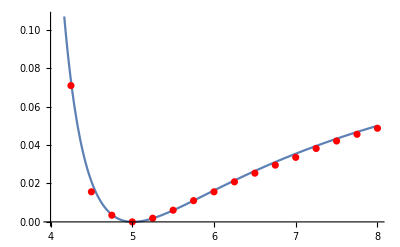

```mathematica
Show[
Plot[(rs-(6 ArcSin[1/(2 δs[α,3])])/π)^2, {α,4,8}],
ListPlot[Table[{α,(rs-Rho[α,3,1])^2}, {α, 4, 8, 0.25}],PlotStyle->Red]
]
```

```mathematica
Clear[α,β,δ]
```

```mathematica
hatqd=Table[QDemp[q, x1, x2], {q,{0.05, 0.1, 0.9, 0.95}}]
```

{0.1724,0.2508,0.2948,0.2236}

```mathematica
target=Flatten[Join[{SpearmanRho[x1, x2]}, hatqd]]
```

{0.373606,0.1724,0.2508,0.2948,0.2236}

```mathematica
f=Flatten[Join[{HoldForm[(6 ArcSin[δ/(2 δs[α,β])])/π]}, Table[HoldForm[QD[q0, α,β,δ,F1]]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]]]
```

{(6 sin^-1(δ/(2 δs(α,β))))/π,QD(0.05,α,β,δ,F1),QD(0.1,α,β,δ,F1),QD(0.9,α,β,δ,F1),QD(0.95,α,β,δ,F1)}

```mathematica
Clear[obj]
```

```mathematica
obj[α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{F1,f,q0,q},
If[δs[α,β]-δ<0,δ-δs[α,β],
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f=Flatten[Join[{(6 ArcSin[δ/(2 δs[α,β])])/π}, Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]]];
Sqrt[Total[(target-f)^2]]
]
]
```

```mathematica
Timing[sol=NMinimize[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {α,β,δ}, Method->"SimulatedAnnealing", PrecisionGoal->1, AccuracyGoal->1]]
```

$Aborted

```mathematica
Timing[sol=NMinimize[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {α,β,δ}, Method->"SimulatedAnnealing", PrecisionGoal->1, AccuracyGoal->1]]
```

{1026.49,{0.0380413,{α→3.63485,β→0.583068,δ→1.3811}}}

```mathematica
Timing[sol=NMinimize[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {α,β,δ}, Method->"SimulatedAnnealing", PrecisionGoal->2, AccuracyGoal->2]]
```

{1329.88,{0.00328921,{α→5.41824,β→3.50391,δ→0.936675}}}

```mathematica
obj[5,3,1]
```

0.00524265

```mathematica
obj[5.41824, 3.50391, 0.936675]
```

0.00328921

## Read BTC data

```mathematica
data=Import[NotebookDirectory[]<> "../processed_data/btc_future_crix.csv"];
```

```mathematica
Dimensions[data]
```

{646,14}

```mathematica
data[[1;;10,12;;13]]
```

(return_btc | return_brr
-0.0226425 | -0.0564519
-0.0667516 | -0.0409618
-0.0522745 | -0.0463652
0.020076 | 0.0120735
0.0174733 | 0.0233977
0.0252517 | 0.0109912
-0.0252517 | -0.012727
0.016472 | 0.00609231
-0.0427781 | -0.0313833)

```mathematica
rbtc=data⟦2;;All,12⟧;
rbrr=data⟦2;;All,13⟧;
```

```mathematica
{Correlation[rbrr,rbtc], SpearmanRho[rbrr, rbtc]}
```

{0.788286,0.733723}

```mathematica
hatqd=Table[QDemp[q, rbrr, rbtc], {q,{0.05, 0.1, 0.9, 0.95}}]
```

{0.55814,0.635659,0.620155,0.589147}

```mathematica
target=Flatten[Join[{SpearmanRho[rbrr, rbtc]}, hatqd]]
```

{0.733723,0.55814,0.635659,0.620155,0.589147}

```mathematica
f=Flatten[Join[{HoldForm[(6 ArcSin[δ/(2 δs[α,β])])/π]}, Table[HoldForm[QD[q0, α,β,δ,F1]]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]]]
```

{(6 sin^-1(δ/(2 δs(α,β))))/π,QD(0.05,α,β,δ,F1),QD(0.1,α,β,δ,F1),QD(0.9,α,β,δ,F1),QD(0.95,α,β,δ,F1)}

```mathematica
Clear[obj]
```

```mathematica
obj[α_?NumericQ,β_?NumericQ,δ_?NumericQ]:=Module[{F1,f,q0,q},
If[δs[α,β]-δ<0,δ-δs[α,β],
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f=Flatten[Join[{(6 ArcSin[δ/(2 δs[α,β])])/π}, Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}]]];
Sqrt[Total[(target-f)^2]]
]
]
```

```mathematica
Timing[sol=NMinimize[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {α,β,δ}, Method->"SimulatedAnnealing", PrecisionGoal->1, AccuracyGoal->1]]
```

{971.181,{0.105295,{α→3.0836,β→-1.35137,δ→1.83593}}}

```mathematica
Timing[sol=NMinimize[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {{α,3,5},{β,0,0.5},{δ,0,4}}, Method->"SimulatedAnnealing", PrecisionGoal->1, AccuracyGoal->1]]
```

{1192.25,{0.0957786,{α→3.58954,β→0.128872,δ→2.98135}}}

```mathematica
δs[α, β]-δ/.sol[[2]]
```

0.601245

```mathematica
Timing[sol=FindMinimum[{obj[α,β,δ],α>3 &&Abs[β]<α&&0< δ<Re[δs[α,β]]}, {{α,3},{β,0.75},{δ,2.25}},PrecisionGoal->1, AccuracyGoal->1]]
```

{365.716,{0.0897212,{α→3.00063,β→0.740852,δ→2.25428}}}

```mathematica
δs[α, β]-δ/.sol[[2]]
```

0.476239

```mathematica
α0=α/.sol⟦2⟧;
β0=β/.sol⟦2⟧;
δ0=δ/.sol⟦2⟧;
```

```mathematica
α0=3.1354; β0=0.121548; δ0=2.53221;
```

```mathematica
α0=3.0836; β0=-1.35137; δ0=1.83593;
```

```mathematica
obj[α0,β0,δ0]
```

0.089721

```mathematica
{Rho[α0,β0,δ0],(6 ArcSin[δ0/(2 δs[α0,β0])])/π,SpearmanRho[rbrr,rbtc]}
```

{0.814971,0.81269,0.733723}

```mathematica
δs[α0,β0]-δ0
```

0.476239

```mathematica
Timing[t1=Table[{α,obj[α, β0,δ0]}, {α,2.6,5, 0.1}]];
```

```mathematica
Timing[t2=Table[{β,obj[α0,β,δ0]}, {β,-1,1, 0.1}]];
```

```mathematica
Timing[t3=Table[{δ,obj[α0,β0,δ]}, {δ,0.1,3.1, 0.25}]];
```

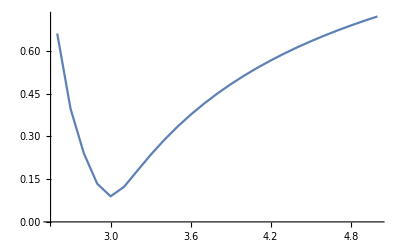
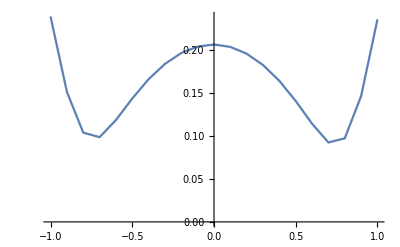
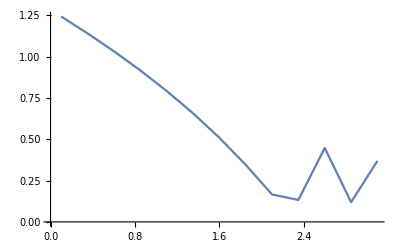

```mathematica
{ListPlot[t1, Joined->True], ListPlot[t2, Joined->True], ListPlot[t3, Joined->True]}
```

Optimise with matching Spearman’s rho constraint

```mathematica
Clear[FNIGi]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
Clear[obj]
```

```mathematica
const=Sin[1/6 target⟦1⟧ π] 2;
obj[α_?NumericQ,β_?NumericQ]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, (*{q,{0.05,0.95}}];*)
{q,{0.05,0.1, 0.9, 0.95}}];
(*Sqrt[Total[(target⟦{2,5}⟧-f)^2]]*)
Sqrt[Total[(target⟦2;;⟧-f)^2]]
]
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
TimeConstrained[Timing[sol=NMinimize[{obj[α,β],α>0 &&Abs[β]<α}, {{α,0.1,1},{β,-0.1,0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1]],1800]
```

$Aborted

```mathematica
(*Timing[sol=FindMinimum[{obj[α,β],α>1 &&Abs[β]<α}, {{α,0.1},{β,0.}},PrecisionGoal->1, AccuracyGoal->1]]*)
```

{701.434,{0.0698849,{α→1.00012,β→0.39475}}}

```mathematica
α0=α/.sol⟦2⟧;
β0=β/.sol⟦2⟧;
α0=0.772993;
β0=0.0293319;
δ0=Sin[1/6 target⟦1⟧ π] 2 δs[α0,β0]
```

0.578178

```mathematica
obj[α0,β0]
```

0.0395157

```mathematica
{Rho[α0,β0,δ0],(6 ArcSin[δ0/(2 δs[α0,β0])])/π,SpearmanRho[rbrr,rbtc]}
```

{0.747028,0.733723,0.733723}

```mathematica
δs[α0,β0]-δ0
```

0.193146

```mathematica
Timing[t1=Table[{α,obj[α, β0]}, {α,0.5,1.2, 0.025}]];
```

```mathematica
Timing[t2=Table[{β,obj[α0,β]}, {β,-.3,.3, 0.025}]];
```

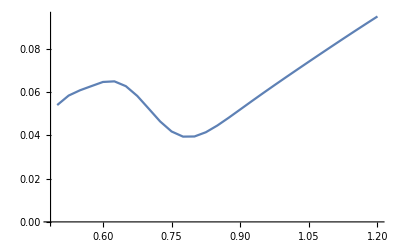
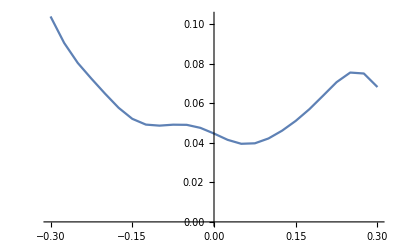

```mathematica
{ListPlot[t1, Joined->True], ListPlot[t2, Joined->True]}
```

```mathematica
s
```

```mathematica
target
```

{0.733723,0.55814,0.635659,0.620155,0.589147}

```mathematica
F1=FNIGi[α0,β0,μs[α0,β0], δs[α0,β0]-δ0];
```

```mathematica
ReleaseHold[f/.{α->α0, β->β0, δ->δ0}]
```

{0.733723,0.587159,0.609982,0.615578,0.595405}

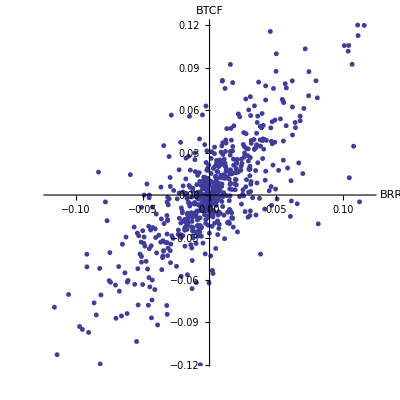

```mathematica
p=ListPlot[{rbrr,rbtc}ᵀ,PlotMarkers->{Automatic,5},PlotTheme->"Classic",BaseStyle->{FontSize->12},AspectRatio->1,AxesLabel->{"BRR", "BTCF"}]
```

```mathematica
Export[NotebookDirectory[] <>"../latex/_pics/scatter.pdf", p]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/scatter.pdf

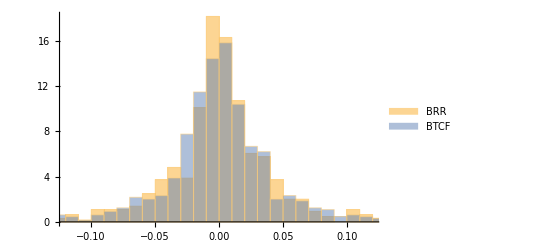

```mathematica
p=Histogram[{rbrr,rbtc}, Automatic, "PDF",ChartLegends->{"BRR", "BTCF"}]
```

```mathematica
Drbrr=EmpiricalDistribution[rbrr];
Drbtc=EmpiricalDistribution[rbtc];
```

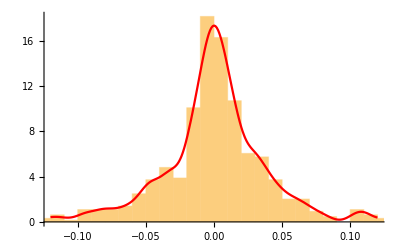
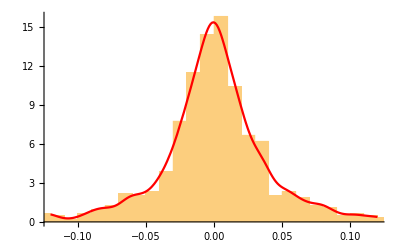

```mathematica
{p1=Show[
Histogram[rbrr, Automatic, "PDF"],
Plot[PDF[SmoothKernelDistribution[rbrr], x], {x,-0.12, 0.12},PlotStyle->Red]
],
p2=Show[
Histogram[rbtc, Automatic, "PDF"],
Plot[PDF[SmoothKernelDistribution[rbtc], x], {x,-0.12, 0.12},PlotStyle->Red]
]
}
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/rbrr.pdf",p1]
Export[NotebookDirectory[] <> "../latex/_pics/rbtc.pdf",p2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rbrr.pdf

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/rbtc.pdf

Make margins uniform using empirical distribution function (not smoothed version)

```mathematica
u=hatF[rbrr, rbrr];
v=hatF[rbtc, rbtc];
```

```mathematica
(*u=Table[CDF[Drbrr, rbrr[[i]]], {i,1,Length[rbrr]}];
v=Table[CDF[Drbtc, rbtc[[i]]], {i,1, Length[rbtc]}];*)
```

Drop largest sample (which has CDF of 1, messing up any sample mean-like computations)

```mathematica
(*u=DeleteCases[u, Max[u]];
v=DeleteCases[v, Max[v]];*)
```

Empirical copula

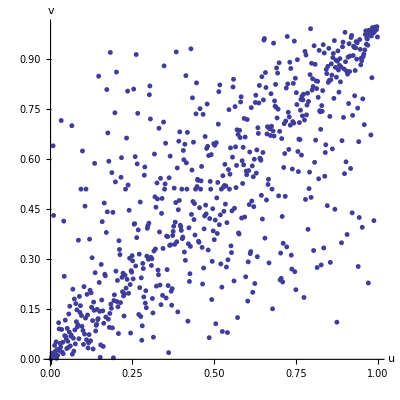

```mathematica
c1=ListPlot[{u,v}ᵀ,AxesLabel->{HoldForm[u], HoldForm[v]},PlotMarkers->{Automatic,5},PlotTheme->"Classic",BaseStyle->{FontSize->12},AspectRatio->1]
```

### Compare with simulated data

```mathematica
α=α0;
β=β0;
δ=δ0;
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
```

```mathematica
SeedRandom[123456];
n=Length[rbrr];
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
```

```mathematica
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
```

```mathematica
{Mean[X1],Mean[X2]}
{Variance[X1], Variance[X2]}
```

{0.0210671,0.0392802}

{0.913135,0.942272}

Correlation

```mathematica
N[{δ/δs[α,β],Correlation[X1,X2]}]
```

{0.749592,0.748078}

Rank correlation

```mathematica
N[{(6 ArcSin[δ/(2 δs[α,β])])/π,(6 ArcSin[1/2 Correlation[X1,X2]])/π,Rho[α,β,δ],SpearmanRho[X1,X2]}]
```

{0.733723,0.732164,0.747028,0.714956}

```mathematica
usim = hatF[X1,X1];
vsim = hatF[X2,X2];
```

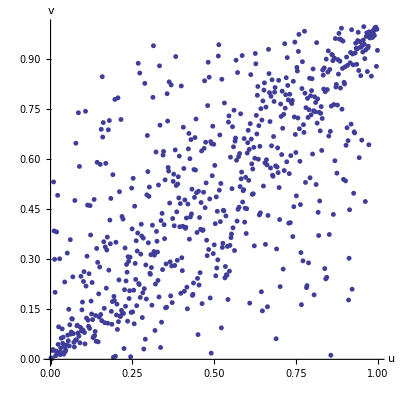

```mathematica
c2=ListPlot[{usim,vsim}ᵀ,AxesLabel->{HoldForm[u], HoldForm[v]},PlotMarkers->{Automatic,5},PlotTheme->"Classic",BaseStyle->{FontSize->12},AspectRatio->1]
```

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copula_nig1.pdf", c1]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copula_nig1.pdf

```mathematica
Export[NotebookDirectory[] <> "../latex/_pics/copula_nig2.pdf", c2]
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../latex/_pics/copula_nig2.pdf